# Making Graphs

## Plot

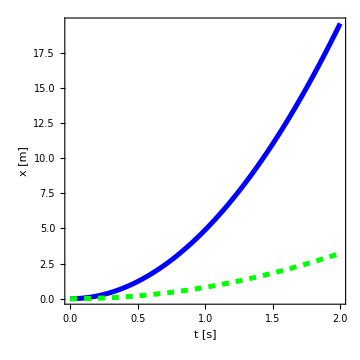

```mathematica
f[t_]=(9.8/2)*t^2;(*The free fall on the Earth*)
g[t_]=(1.62/2)*t^2;(*The free fall on the Moon*)
Plot[{f[t],g[t]},{t,0,2},
PlotStyle->{Directive[Blue,Thickness[0.01]],Directive[Green,Thickness[0.01],Dashed]},
PlotRange->{{0,2},{f[0],f[2]}},
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{Row[{Style["t",Italic,20,Black,FontFamily->"Times New Roman"],Style[" [s]",20,Black,FontFamily->"Times New Roman"]}],Row[{Style["x",Italic,20,Black,FontFamily->"Times New Roman"],Style[" [m]",20,Black,FontFamily->"Times New Roman"]}]},
FrameTicksStyle->Directive[Black,FontSize->20,  FontFamily->"Times New Roman"],
ImageSize->Medium]
```